## Enhancing transport by shaping barriers

### Double well potential

{{x→-0.06},{x→-0.17},{x→-0.28},{x→-0.39},{x→-0.5}}

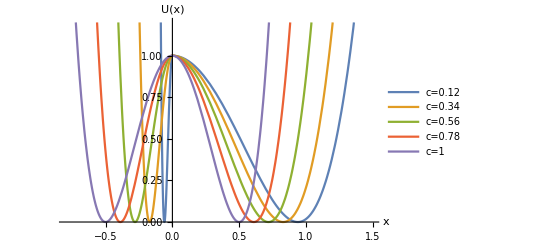

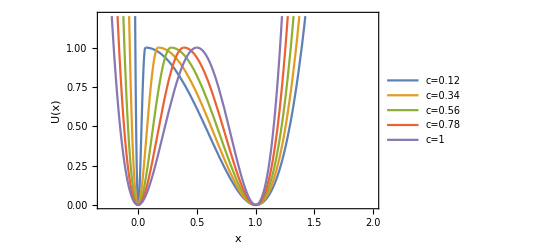

```mathematica
U[x_,c_]:=h(1-(2 x/s[x,c])^2)^2;
s[x_,c_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x]
(* s[x_,c_]:=c θ[-x]+(2-c) θ[x];
θ[x_]:=1/(1+Exp[-2 k x]) (* heaviside step function *) *)
k=50;
h=1;
cValues={0.12,0.34,0.56,0.78,1.00};
Evaluate[Table[Last[FindMinimum[U[x,c],{x,-0.3}]],{c,cValues}]]
Plot[Evaluate[Table[U[x,c],{c,cValues}]],{x,-0.8,1.5},PlotRange->{0,1.2},AxesLabel->{"x","U(x)"},PlotLegends->{"c=0.12","c=0.34","c=0.56","c=0.78","c=1"}]
(* next plot shifts functions to the right so that minima coincide *)
Plot[{U[x-0.0618154,0.12],U[x-0.17,0.34],U[x-0.28,0.56],U[x-0.39,0.78],U[x-0.5,1]},{x,-0.3,2},Frame->True,PlotRange->{0,1.2},FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium,LabelStyle->Medium,PlotLegends->Placed[LineLegend[{"c=0.12","c=0.34","c=0.56","c=0.78","c=1"},LegendLayout->{"Row",5}],{Right,Bottom}]]
```

#### Double well potential: calculation of MFPT from left to right well

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.483191,0.467529,0.452949,0.43939,0.4268,0.415127,0.404328,0.394364,0.385199,0.376801,0.369145,0.362207,0.355967,0.350409,0.345523,0.341299,0.337731,0.334819,0.332565,0.330974,0.330056,0.329823,0.330293,0.331487,0.33343,0.336153,0.339689,0.344079,0.349368,0.355605,0.362848,0.371161,0.380614,0.391284,0.403259,0.416633,0.431512,0.44801,0.466255,0.486386,0.508556,0.532932,0.559698,0.589054,0.621221,0.65644,0.694975,0.737113,0.78317,0.833493}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.4874,0.475966,0.465649,0.456409,0.448209,0.441019,0.434815,0.429577,0.42529,0.421948,0.419545,0.418082,0.417567,0.418011,0.419431,0.421849,0.425295,0.429802,0.435411,0.442168,0.450128,0.459351,0.469906,0.48187,0.495328,0.510377,0.527121,0.545676,0.566172,0.588748,0.61356,0.640777,0.670585,0.703189,0.738811,0.777694,0.820106,0.866338,0.916708,0.971563,1.03128,1.09628,1.16702,1.24398,1.3277,1.41879,1.51787,1.62565,1.7429,1.87046}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.491803,0.484792,0.478936,0.474214,0.470611,0.468116,0.466726,0.466443,0.467277,0.469241,0.472357,0.476653,0.482162,0.488927,0.496996,0.506424,0.517277,0.529627,0.543555,0.559154,0.576525,0.595781,0.617046,0.640458,0.666169,0.694345,0.725167,0.758837,0.795572,0.835611,0.879218,0.926676,0.9783,1.03443,1.09544,1.16173,1.23375,1.31198,1.39695,1.48924,1.58947,1.69834,1.81658,1.94502,2.08456,2.23615,2.40087,2.57988,2.77443,2.98592}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.496207,0.493617,0.492222,0.492019,0.493013,0.495213,0.498637,0.50331,0.509263,0.516534,0.52517,0.535224,0.546758,0.559844,0.574561,0.590999,0.609258,0.629451,0.651699,0.676139,0.702921,0.73221,0.764186,0.799047,0.83701,0.878313,0.923214,0.971998,1.02497,1.08248,1.14488,1.21248,1.28592,1.36567,1.45206,1.54576,1.64739,1.75762,1.87719,2.00691,2.14766,2.30039,2.46615,2.64608,2.84142,3.05352,3.28388,3.53411,3.80596,4.10138}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.50061,0.502443,0.505509,0.509825,0.515415,0.52231,0.530549,0.540178,0.55125,0.563828,0.577983,0.593795,0.611354,0.63076,0.652126,0.675574,0.70124,0.729275,0.759843,0.793125,0.829318,0.86864,0.911326,0.957636,1.00785,1.06228,1.12126,1.18516,1.25437,1.32934,1.41053,1.49848,1.59373,1.69691,1.80869,1.92979,2.06103,2.20326,2.35743,2.52459,2.70585,2.90244,3.11572,3.34713,3.59827,3.87089,4.16689,4.48833,4.83749,5.21683}

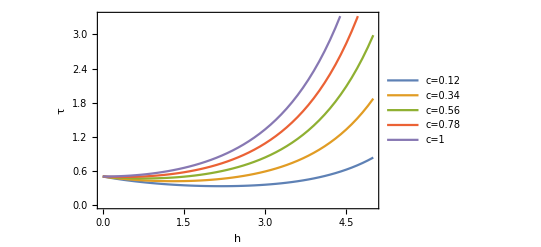

```mathematica
ClearAll[U,s,Ushift,τ,sol,h,c]

U[x_]:=h(1-(2 x/s[x])^2)^2;
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

hMin=0;
hMax=5;
hStepsize=0.1;

(* c=0.12 *)
τc012={};
c=0.12;
Ushift[x_]=U[x-0.0618154];
Do[sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc012,τ],{h,hMin,hMax,hStepsize}]
Print[τc012]

(* c=0.34 *)
τc034={};
c=0.34;
Ushift[x_]=U[x-0.17];
Do[sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc034,τ],{h,hMin,hMax,hStepsize}]
Print[τc034]

(* c=0.56 *)
τc056={};
c=0.56;
Ushift[x_]=U[x-0.28];
Do[sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc056,τ],{h,hMin,hMax,hStepsize}]
Print[τc056]

(* c=0.78 *)
τc078={};
c=0.78;
Ushift[x_]=U[x-0.39];
Do[sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc078,τ],{h,hMin,hMax,hStepsize}]
Print[τc078]

(* c=1 *)
τc1={};
c=1;
Ushift[x_]=U[x-0.5];
Do[sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc1,τ],{h,hMin,hMax,hStepsize}]
Print[τc1]

ListLinePlot[{Transpose@{Range[hMin,hMax,hStepsize],τc012},Transpose@{Range[hMin,hMax,hStepsize],τc034},Transpose@{Range[hMin,hMax,hStepsize],τc056},Transpose@{Range[hMin,hMax,hStepsize],τc078},Transpose@{Range[hMin,hMax,hStepsize],τc1}},Frame->True,FrameLabel->{"h","τ"},Axes->False,LabelStyle->Medium,LabelStyle->Medium,PlotLegends->Placed[LineLegend[{"c=0.12","c=0.34","c=0.56","c=0.78","c=1"},LegendLayout->{"Row",5}],{Left,Top}]]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindArgMin::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.33826,0.340712,0.343164,0.345616,0.348068,0.35052,0.352972,0.355424,0.357875,0.360328,0.36278,0.365232,0.367684,0.370136,0.372588,0.37504,0.377492,0.379944,0.382396,0.384848,0.3873,0.389752,0.392204,0.394656,0.397108,0.39956,0.402012,0.404464,0.406916,0.409368,0.41182,0.414272,0.416724,0.419177,0.421628,0.424081,0.426533,0.428985,0.431437,0.433889,0.436341,0.438793,0.441245,0.443697,0.446149,0.448601,0.451053,0.453505,0.455957,0.458409,0.460861,0.463313,0.465765,0.468217,0.470669,0.473121,0.475573,0.478025,0.480478,0.482929,0.485381,0.487834,0.490285,0.492737,0.495189,0.497641,0.500093,0.502545,0.504997,0.507449,0.509901,0.512353,0.514805,0.517257,0.519709,0.522161,0.524613,0.527065,0.529518,0.53197,0.534421,0.536874,0.539325,0.541778,0.54423,0.546682,0.549134,0.551586,0.554038,0.556488,0.558942,0.561394,0.563846,0.566298,0.56875,0.571202,0.573654,0.576106,0.578558,0.58101}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindArgMin::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.245005,0.252106,0.259208,0.26631,0.273412,0.280513,0.287615,0.294717,0.301818,0.30892,0.316022,0.323123,0.330225,0.337327,0.344428,0.35153,0.358632,0.365733,0.372835,0.379937,0.387038,0.39414,0.401242,0.408343,0.415445,0.422547,0.429649,0.43675,0.443852,0.450953,0.458055,0.465157,0.472258,0.47936,0.486462,0.493564,0.500665,0.507767,0.514868,0.52197,0.529071,0.536173,0.543275,0.550377,0.557479,0.56458,0.571683,0.578784,0.585885,0.592987,0.600089,0.607191,0.614292,0.621393,0.628495,0.635597,0.642698,0.649801,0.656902,0.664004,0.671105,0.678207,0.685308,0.69241,0.699512,0.706613,0.713715,0.720817,0.727919,0.73502,0.742122,0.749224,0.756326,0.763427,0.770529,0.77763,0.784732,0.791834,0.798935,0.806037,0.813139,0.820241,0.827342,0.834444,0.841546,0.848647,0.855748,0.86285,0.869952,0.877053,0.884156,0.891257,0.898359,0.905461,0.912562,0.919664,0.926766,0.933867,0.940969,0.948071}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindArgMin::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.201227,0.218944,0.236661,0.254378,0.272095,0.289812,0.307529,0.325245,0.342962,0.360679,0.378396,0.396113,0.41383,0.431547,0.449264,0.466981,0.484698,0.502415,0.520132,0.537849,0.555566,0.573283,0.591,0.608716,0.626433,0.64415,0.661867,0.679583,0.697301,0.715018,0.732735,0.750452,0.768169,0.785886,0.803603,0.821319,0.839036,0.856753,0.87447,0.892187,0.909904,0.927621,0.945338,0.963055,0.980772,0.998489,1.01621,1.03392,1.05164,1.06936,1.08707,1.10479,1.12251,1.14022,1.15794,1.17566,1.19337,1.21109,1.22881,1.24653,1.26424,1.28196,1.29968,1.31739,1.33511,1.35283,1.37054,1.38826,1.40598,1.42369,1.44141,1.45913,1.47685,1.49456,1.51228,1.53,1.54771,1.56543,1.58315,1.60086,1.61858,1.6363,1.65401,1.67173,1.68945,1.70717,1.72488,1.7426,1.76032,1.77803,1.79575,1.81347,1.83118,1.8489,1.86662,1.88434,1.90205,1.91977,1.93749,1.9552}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindArgMin::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.192902,0.221327,0.249751,0.278175,0.3066,0.335024,0.363448,0.391873,0.420297,0.448721,0.477145,0.505569,0.533994,0.562418,0.590842,0.619265,0.647691,0.676115,0.70454,0.732964,0.761388,0.789812,0.818237,0.846661,0.875085,0.90351,0.931933,0.960358,0.988782,1.01721,1.04563,1.07406,1.10248,1.1309,1.15933,1.18775,1.21618,1.2446,1.27303,1.30145,1.32987,1.3583,1.38672,1.41515,1.44357,1.47199,1.50042,1.52884,1.55727,1.58569,1.61412,1.64254,1.67097,1.69939,1.72781,1.75624,1.78466,1.81309,1.84151,1.86994,1.89836,1.92678,1.95521,1.98363,2.01206,2.04048,2.06891,2.09733,2.12575,2.15418,2.1826,2.21103,2.23945,2.26788,2.2963,2.32472,2.35315,2.38157,2.41,2.43842,2.46684,2.49527,2.52369,2.55212,2.58054,2.60897,2.63739,2.66582,2.69424,2.72266,2.75109,2.77951,2.80794,2.83636,2.86479,2.89321,2.92163,2.95006,2.97848,3.00691}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindArgMin::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.195323,0.241484,0.287646,0.333807,0.37997,0.426131,0.472293,0.518454,0.564616,0.610778,0.656939,0.703101,0.749262,0.795424,0.841586,0.887743,0.933909,0.980071,1.02623,1.07239,1.11856,1.16472,1.21088,1.25704,1.3032,1.34936,1.39552,1.44169,1.48785,1.53401,1.58017,1.62633,1.6725,1.71866,1.76482,1.81098,1.85714,1.9033,1.94947,1.99563,2.04179,2.08795,2.13411,2.18027,2.22644,2.2726,2.31876,2.36492,2.41108,2.45725,2.50341,2.54957,2.59573,2.64189,2.68805,2.73421,2.78037,2.82654,2.8727,2.91886,2.96502,3.01118,3.05734,3.1035,3.14967,3.19583,3.24199,3.28815,3.33431,3.38048,3.42664,3.4728,3.51896,3.56512,3.61128,3.65745,3.70361,3.74977,3.79593,3.84209,3.88825,3.93442,3.98058,4.02674,4.0729,4.11906,4.16522,4.21139,4.25755,4.30371,4.34987,4.39603,4.44219,4.48836,4.53452,4.58068,4.62684,4.67301,4.71916,4.76533}

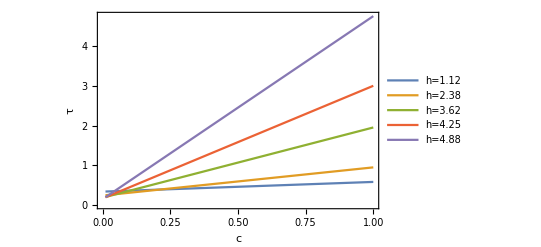

```mathematica
ClearAll[U,s,Ushift,τ,sol,c,h]

U[x_]:=h(1-(2 x/s[x])^2)^2;
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

cMin=0.01;
cMax=1;
cStepsize=0.01;

(* h=1.12 *)
τh112={};
h=1.12;
Do[min=##&@@FindArgMin[U[x],{x,-0.3}];Ushift[x_]=U[x+min];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh112,τ],{c,cMin,cMax,cStepsize}]
Print[τh112]

(* h=2.38 *)
τh238={};
h=2.38;
Do[min=##&@@FindArgMin[U[x],{x,-0.3}];Ushift[x_]=U[x+min];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh238,τ],{c,cMin,cMax,cStepsize}]
Print[τh238]

(* h=3.62 *)
τh362={};
h=3.62;
Do[min=##&@@FindArgMin[U[x],{x,-0.3}];Ushift[x_]=U[x+min];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh362,τ],{c,cMin,cMax,cStepsize}]
Print[τh362]

(* h=4.25 *)
τh425={};
h=4.25;
Do[min=##&@@FindArgMin[U[x],{x,-0.3}];Ushift[x_]=U[x+min];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh425,τ],{c,cMin,cMax,cStepsize}]
Print[τh425]

(* h=4.88 *)
τh488={};
h=4.88;
Do[min=##&@@FindArgMin[U[x],{x,-0.3}];Ushift[x_]=U[x+min];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x]] NIntegrate[Exp[Ushift[y]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh488,τ],{c,cMin,cMax,cStepsize}]
Print[τh488]


ListLinePlot[{Transpose@{Range[cMin,cMax,cStepsize],τh112},Transpose@{Range[cMin,cMax,cStepsize],τh238},Transpose@{Range[cMin,cMax,cStepsize],τh362},Transpose@{Range[cMin,cMax,cStepsize],τh425},Transpose@{Range[cMin,cMax,cStepsize],τh488}},Frame->True,FrameLabel->{"c","τ"},Axes->False,LabelStyle->Medium,LabelStyle->Medium,PlotLegends->Placed[LineLegend[{"h=1.12","h=2.38","h=3.62","h=4.25","h=4.88"},LegendLayout->{"Row",5}],{Left,Top}]]
```

### Creating extra equilibrium state in double well potential by manipulation

The potential function U(x) is multiplied by a function g(x)

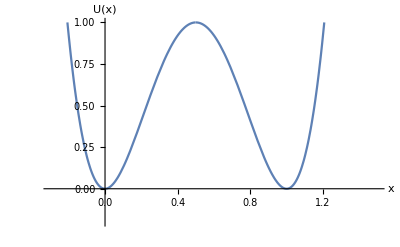

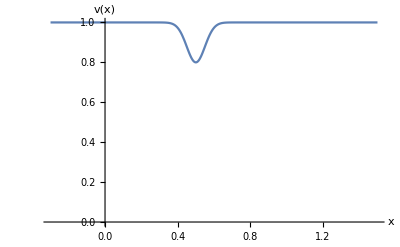

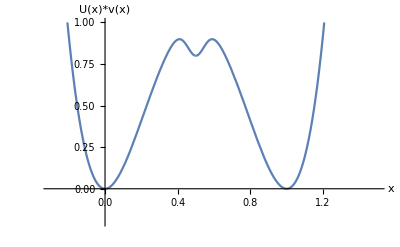

```mathematica
U[x_,c_]:=h(1-(2 x/s[x,c])^2)^2;
s[x_,c_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x]
v[x_]:=1-0.2 Exp[-200 (x-0.5)^2]

h=1;
c=1;

Plot[U[x-0.5,1],{x,-0.3,1.5},PlotRange->{-0.2,1},AxesLabel->{"x","U(x)"}]
Plot[v[x],{x,-0.3,1.5},PlotRange->{0,1},AxesLabel->{"x","v(x)"}]
Plot[U[x-0.5,1]*v[x],{x,-0.3,1.5},PlotRange->{-0.2,1},AxesLabel->{"x","U(x)*v(x)"}]
```

-Graphics-

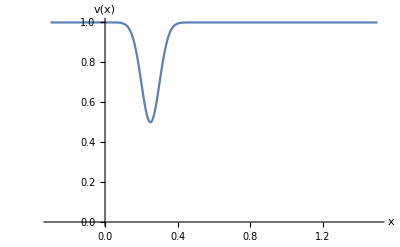

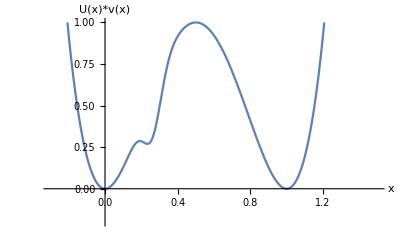

```mathematica
U[x_,c_]:=h(1-(2 x/s[x,c])^2)^2;
s[x_,c_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x]
v[x_]:=1- 0.5 Exp[-200 (x-0.25)^2]

h=1;
c=1;

Plot[U[x-0.5,1],{x,-0.3,1.5},PlotRange->{-0.2,1},AxesLabel->{"x","U(x)"}]
Plot[v[x],{x,-0.3,1.5},PlotRange->{0,1},AxesLabel->{"x","v(x)"}]
Plot[U[x-0.5,1]*v[x],{x,-0.3,1.5},PlotRange->{-0.2,1},AxesLabel->{"x","U(x)*v(x)"}]
```

-Graphics-

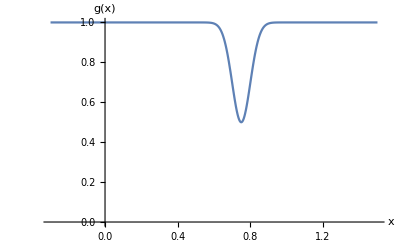

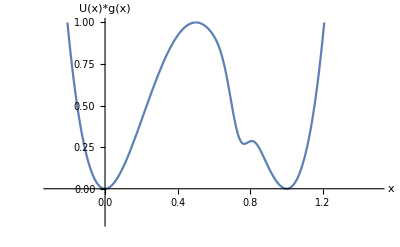

```mathematica
U[x_,c_]:=h(1-(2 x/s[x,c])^2)^2;
s[x_,c_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x]
v[x_]:=1- 0.5 Exp[-200 (x-0.75)^2]

h=1;
c=1;

Plot[U[x-0.5,1],{x,-0.3,1.5},PlotRange->{-0.2,1},AxesLabel->{"x","U(x)"}]
Plot[v[x],{x,-0.3,1.5},PlotRange->{0,1},AxesLabel->{"x","v(x)"}]
Plot[U[x-0.5,1]*v[x],{x,-0.3,1.5},PlotRange->{-0.2,1},AxesLabel->{"x","U(x)*v(x)"}]
```

### Comparison original and manipulated potentials (without normalized height)

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.515415,0.563828,0.652126,0.793125,1.00785,1.32934,1.80869,2.52459,3.59827,5.21683}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.512029,0.549441,0.616397,0.720454,0.873601,1.09393,1.40814,1.85541,2.49297,3.40453}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.517149,0.562561,0.641611,0.764153,0.946161,1.21243,1.60086,2.16919,3.00538,4.24384}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.5,0.509344,0.546743,0.617356,0.730811,0.902832,1.15794,1.53373,2.08758,2.90703,4.12601}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.37997,0.610778,0.841586,1.07239,1.3032,1.53401,1.76482,1.99563,2.22644,2.45725,2.68805,2.91886,3.14967,3.38048,3.61128,3.84209,4.0729,4.30371,4.53452,4.76533}

{0.364727,0.506643,0.654364,0.801265,0.948082,1.095,1.24199,1.38903,1.53605,1.68303,1.82997,1.97688,2.12378,2.2707,2.41768,2.56476,2.71198,2.8594,3.00705,3.15499}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.416311,0.639232,0.850399,1.04901,1.23684,1.41701,1.59266,1.7663,1.93957,2.1134,2.28819,2.46408,2.64101,2.8189,2.99764,3.17711,3.35721,3.53784,3.71892,3.90038}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.346746,0.528705,0.710606,0.892443,1.07421,1.2559,1.43751,1.61902,1.80044,1.98175,2.16294,2.34401,2.52494,2.70573,2.88638,3.06688,3.24723,3.42744,3.60753,3.78751}

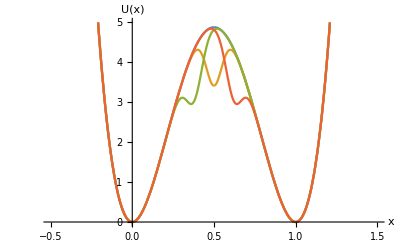

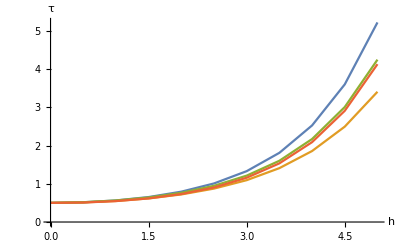

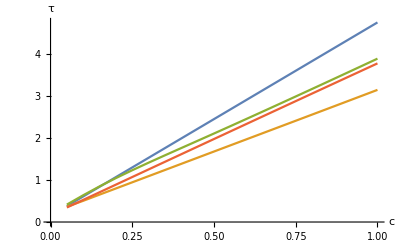

```mathematica
ClearAll[U,s,Ushift]

hMin=0;
hMax=5;
hStepsize=0.5;

cMin=0.05;
cMax=1;
cStepsize=0.05;

a=0.3;
b=200;

c1=1;
h488=4.88;

(* original potential function *)
U[x_,c_,h_]:=h(1-(2 x/s[x,c])^2)^2;
s[x_,c_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

(* potential function with perturbation *)
Uper[x_,c_,h_,d_]:=h(1-(2 x/s[x,c])^2)^2 (1-a Exp[-b (x+d)^2]);

(* varying h for original potential function *)
τc1or={};
Do[Ushift[x_,c_,h_]=U[x-0.5,c1,h];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c1,h]] NIntegrate[Exp[Ushift[y,c1,h]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc1or,τ],{h,hMin,hMax,hStepsize}]
Print[τc1or]

(* varying h for potential function with perturbation in the middle *)
τc1perM={};
dM=0;
Do[Ushift[x_,c_,h_,d_]=Uper[x-0.5,c1,h,dM];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c1,h,dM]] NIntegrate[Exp[Ushift[y,c1,h,dM]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc1perM,τ],{h,hMin,hMax,hStepsize}]
Print[τc1perM]

(* varying h for potential function with perturbation on the left of the peak *)
τc1perL={};
dL=(1/4)*0.5;
Do[Ushift[x_,c_,h_,d_]=Uper[x-0.5,c1,h,dL];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c1,h,dL]] NIntegrate[Exp[Ushift[y,c1,h,dL]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc1perL,τ],{h,hMin,hMax,hStepsize}]
Print[τc1perL]

(* varying h for potential function with perturbation on the right of the peak *)
τc1perR={};
dR=-(1/4)*0.5;
Do[sol=FindRoot[Ushift[x_,c_,h_,d_]=Uper[x-0.5,c1,h,dR];τ==NIntegrate[Exp[-Ushift[x,c1,h,dR]] NIntegrate[Exp[Ushift[y,c1,h,dR]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τc1perR,τ],{h,hMin,hMax,hStepsize}]
Print[τc1perR]

(* varying c for original potential function *)
τh488or={};
Do[min=-0.5 c;Ushift[x_,c_,h_]=U[x+min,c,h488];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c,h488]] NIntegrate[Exp[Ushift[y,c,h488]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh488or,τ],{c,cMin,cMax,cStepsize}]
Print[τh488or]

(* varying c for potential function with perturbation in the middle *)
τh488perM={};
Quiet[Do[Clear[d];min=-0.5 c;Ushift[x_,c_,h_,d_]=Uper[x+min,c,h488,d];
x0lim=Which[c<0.25,0.15,c≥0.25&&c<0.45,0.25,c≥0.45&&c<0.65,0.35,c≥0.65&&c<0.85,0.45,c≥0.85&&c<1,0.52,c==1,0.5];
x0lower=Which[c<0.25,0.05,c≥0.25&&c<0.45,0.15,c≥0.45&&c<0.65,0.2,c≥0.65&&c<0.85,0.3,c≥0.85&&c<1,0.4,c==1,0.4];
x0higher=Which[c<0.25,0.3,c≥0.25&&c<0.45,0.4,c≥0.45&&c<0.65,0.5,c≥0.65&&c<0.85,0.6,c≥0.85&&c<1,0.7,c==1,0.6];d0=Which[c<0.25,-0.07,c≥0.25&&c<0.45,-0.06,c≥0.45&&c<0.65,-0.04,c≥0.65&&c<0.85,-0.02,c≥0.85&&c<1,-0.01,c==1,0];
sol1=FindRoot[FindMaxValue[{Ushift[x,c,h488,d],x<x0lim},{x,x0lower}]==FindMaxValue[{Ushift[x,c,h488,d],x>x0lim},{x,x0higher}],{d,d0}];d=d/.sol1;
sol2=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c,h488,d]] NIntegrate[Exp[Ushift[y,c,h488,d]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol2;AppendTo[τh488perM,τ],{c,cMin,cMax,cStepsize}]]
Print[τh488perM]

(* varying c for potential function with perturbation on the left of the peak *)
τh488perL={};
Do[Clear[d];
min=-0.5 c;
(* d=(1/4) min; *)
d=-(1/4) min;
Ushift[x_,c_,h_,d_]=Uper[x+min,c,h488,d];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c,h488,d]] NIntegrate[Exp[Ushift[y,c,h488,d]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh488perL,τ],{c,cMin,cMax,cStepsize}]
Print[τh488perL]

(* varying c for potential function with perturbation on the right of the peak *)
τh488perR={};
Do[min=-0.5 c;
d=-(1/4) (1+min);
Ushift[x_,c_,h_,d_]=Uper[x+min,c,h488,d];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c,h488,d]] NIntegrate[Exp[Ushift[y,c,h488,d]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τh488perR,τ],{c,cMin,cMax,cStepsize}]
Print[τh488perR]

(* Plot potentials *)
Plot[{U[x-0.5,c1,h488],Uper[x-0.5,c1,h488,0],Uper[x-0.5,c1,h488,dL],Uper[x-0.5,c1,h488,dR]},{x,-0.5,1.5},AxesLabel->{"x", "U(x)"},PlotRange->{0,5}]

(* Plot varying h *)
ListLinePlot[{Transpose@{Range[hMin,hMax,hStepsize],τc1or},Transpose@{Range[hMin,hMax,hStepsize],τc1perM},Transpose@{Range[hMin,hMax,hStepsize],τc1perL},Transpose@{Range[hMin,hMax,hStepsize],τc1perR}},AxesLabel->{"h","τ"}]

(* Plot varying c *)
ListLinePlot[{Transpose@{Range[cMin,cMax,cStepsize],τh488or},Transpose@{Range[cMin,cMax,cStepsize],τh488perM},Transpose@{Range[cMin,cMax,cStepsize],τh488perL},Transpose@{Range[cMin,cMax,cStepsize],τh488perR}},AxesLabel->{"c","τ"}]
```

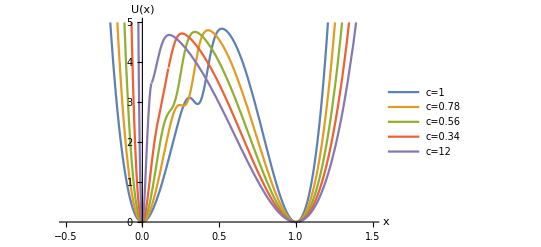

```mathematica
(* potential function with perturbation *)
Uper[x_,c_,h_,d_]:=h(1-(2 x/s[x,c])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_,c_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

a=0.3;
b=200;
h488=4.88;

c1=1;
c078=0.78;
c056=0.56;
c034=0.34;
c012=0.12;
Plot[{Uper[x-0.5 c1,c1,h488,-(1/4)*-0.5 c1],Uper[x-0.5 c078,c078,h488,-(1/4)*-0.5 c078],Uper[x-0.5 c056,c056,h488,-(1/4)*-0.5 c056],Uper[x-0.5 c034,c034,h488,-(1/4)*-0.5 c034],Uper[x-0.5 c012,c012,h488,-(1/4)*-0.5 c012]},{x,-0.5,1.5},AxesLabel->{"x", "U(x)"},PlotRange->{0,5},PlotLegends->{"c=1","c=0.78","c=0.56","c=0.34","c=12"}]
```

#### MFPT changing a (without normalized height)

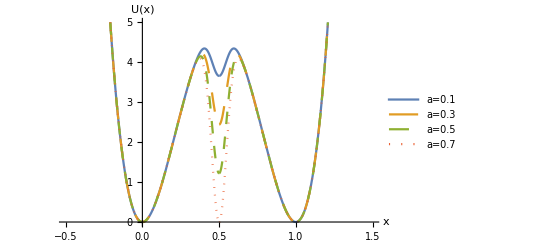

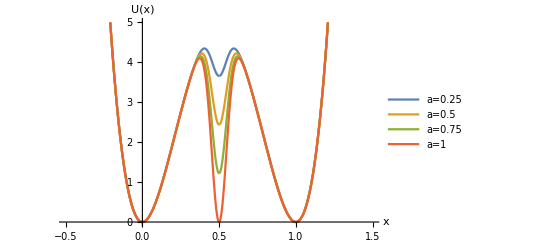

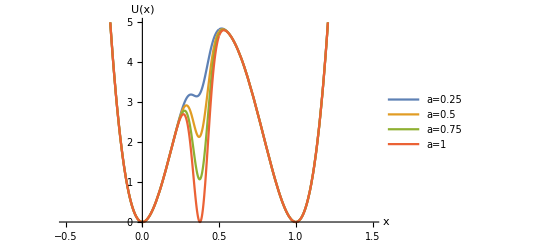

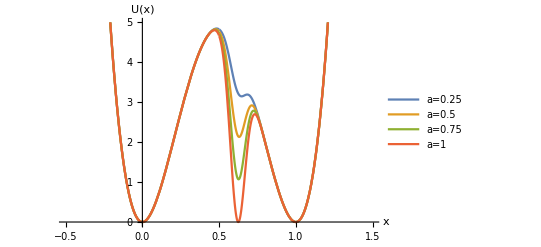

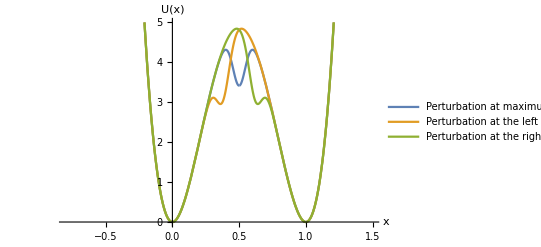

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{4.76533,4.36803,4.03557,3.75646,3.52141,3.32293,3.15499,3.01277,2.89238,2.7908,2.70566,2.63518,2.57813,2.53371,2.50162,2.48195,2.4753,2.48275,2.50594,2.54716,2.60949}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{4.76533,4.55357,4.37412,4.2224,4.09473,3.98815,3.90038,3.82968,3.77482,3.73505,3.71008,3.70004,3.70553,3.72763,3.76797,3.82875,3.91287,4.02402,4.16686,4.34716,4.57206}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{4.76533,4.5377,4.3418,4.17263,4.02605,3.89863,3.78751,3.69032,3.6051,3.53021,3.46434,3.40637,3.35542,3.3108,3.27195,3.23848,3.21013,3.18678,3.16841,3.15517,3.14732}

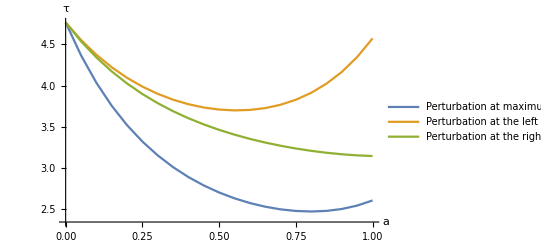

```mathematica
Uper[x_,c_,h_,d_,a_]:=h(1-(2 x/s[x,c])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_,c_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

aValues={0.25,0.5,0.75,1};
aMin=0;
aMax=1.0;
aStepsize=0.05;
b=200;
c=1;
h=4.88;
min=-0.5 c;
d=0;

dL=(1/4)*0.5;
dR=-(1/4)*0.5;
dM=0;

Plot[Evaluate[Table[Uper[x-0.5,c,h,d,a],{a,aValues}]],{x,-0.5,1.5},PlotRange->{0,5},AxesLabel->{"x","U(x)"},PlotLegends->{"a=0.1","a=0.3","a=0.5","a=0.7"},PlotStyle->{Line,Dashing[Large],Dashing[Medium],Dotted}]

Plot[Evaluate[Table[Uper[x-0.5,c,h,d,a],{a,aValues}]],{x,-0.5,1.5},PlotRange->{0,5},AxesLabel->{"x","U(x)"},PlotLegends->{"a=0.25","a=0.5","a=0.75","a=1"}]

Plot[Evaluate[Table[Uper[x-0.5,c,h,dL,a],{a,aValues}]],{x,-0.5,1.5},PlotRange->{0,5},AxesLabel->{"x","U(x)"},PlotLegends->{"a=0.25","a=0.5","a=0.75","a=1"}]

Plot[Evaluate[Table[Uper[x-0.5,c,h,dR,a],{a,aValues}]],{x,-0.5,1.5},PlotRange->{0,5},AxesLabel->{"x","U(x)"},PlotLegends->{"a=0.25","a=0.5","a=0.75","a=1"}]

Plot[{Uper[x-0.5,c,h,dM,0.3],Uper[x-0.5,c,h,dL,0.3],Uper[x-0.5,c,h,dR,0.3]},{x,-0.8,1.5},PlotRange->{0,5},AxesLabel->{"x","U(x)"},PlotLegends->{"Perturbation at maximum","Perturbation at the left of the maximum","Perturbation at the right of the maximum"}]

(* varying a for potential function with perturbation in the middle *)
τaPerM={};
Do[Ushift[x_,c_,h_,d_,a_]=Uper[x-0.5,c1,h,dM,a];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c1,h,dM,a]] NIntegrate[Exp[Ushift[y,c1,h,dM,a]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τaPerM,τ],{a,aMin,aMax,aStepsize}]
Print[τaPerM]

(* varying a for potential function with perturbation on the left of the peak *)
τaPerL={};
Do[Ushift[x_,c_,h_,d_,a_]=Uper[x-0.5,c1,h,dL,a];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,c1,h,dL,a]] NIntegrate[Exp[Ushift[y,c1,h,dL,a]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τaPerL,τ],{a,aMin,aMax,aStepsize}]
Print[τaPerL]

(* varying a for potential function with perturbation on the right of the peak *)
τaPerR={};
Do[sol=FindRoot[Ushift[x_,c_,h_,d_,a_]=Uper[x-0.5,c1,h,dR,a];τ==NIntegrate[Exp[-Ushift[x,c1,h,dR,a]] NIntegrate[Exp[Ushift[y,c1,h,dR,a]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τaPerR,τ],{a,aMin,aMax,aStepsize}]
Print[τaPerR]

ListLinePlot[{Transpose@{Range[aMin,aMax,aStepsize],τaPerM},Transpose@{Range[aMin,aMax,aStepsize],τaPerL},Transpose@{Range[aMin,aMax,aStepsize],τaPerR}},AxesLabel->{"a","τ"},PlotLegends->{"Perturbation at maximum","Perturbation at the left of the maximum","Perturbation at the right of the maximum"}]
```

```mathematica
Uper[x_,d_,a_]:=h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

a=0.2;
b=200;
c=1;
h=4.88;

aStepsize=-0.1;
dStepsize=-0.1;

(* varying a for potential function with perturbation in the middle *)
Ushift[x_,d_,a_]:=Uper[x-0.5,d,a];sol[x_,d_,a_]:=FindRoot[τ==NIntegrate[Exp[-Ushift[x,d,a]] NIntegrate[Exp[Ushift[y,d,a]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ[x_,d_,a_]:=τ/.sol[x,d,a];

yticks=MapIndexed[{#2[[1]],#}&,Range[1,0,aStepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[0.4,-0.4,dStepsize]];

data=Table[τ[x,d,a],{a,1,0,aStepsize},{d,0.4,-0.4,dStepsize}]
dataRounded=Round[data,0.01];
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"d",None},{"a",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]}]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{6.55778,7.4141,6.19529,4.02981,2.60949,2.89558,3.93727,4.56236,4.73505},{6.32407,6.90205,5.64646,3.68915,2.50594,2.90675,3.96189,4.57241,4.73731},{6.10473,6.47115,5.24986,3.48799,2.4753,2.9451,3.99479,4.58415,4.73972},{5.89882,6.10822,4.96776,3.3874,2.50162,3.00882,4.03644,4.5977,4.74229},{5.70543,5.80243,4.77329,3.36384,2.57813,3.09916,4.08789,4.61323,4.74502},{5.52372,5.54483,4.64763,3.40497,2.70566,3.22037,4.15082,4.63097,4.74792},{5.35294,5.32809,4.57813,3.5074,2.89238,3.38023,4.22771,4.65121,4.751},{5.19235,5.14621,4.55704,3.67579,3.15499,3.59108,4.32199,4.67429,4.75427},{5.04129,4.99428,4.58063,3.92344,3.52141,3.87157,4.43838,4.70064,4.75774},{4.89914,4.86837,4.64886,4.27404,4.03557,4.24936,4.58327,4.73077,4.76142},{4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533}}

{{6.56,7.41,6.2,4.03,2.61,2.9,3.94,4.56,4.74},{6.32,6.9,5.65,3.69,2.51,2.91,3.96,4.57,4.74},{6.1,6.47,5.25,3.49,2.48,2.95,3.99,4.58,4.74},{5.9,6.11,4.97,3.39,2.5,3.01,4.04,4.6,4.74},{5.71,5.8,4.77,3.36,2.58,3.1,4.09,4.61,4.75},{5.52,5.54,4.65,3.4,2.71,3.22,4.15,4.63,4.75},{5.35,5.33,4.58,3.51,2.89,3.38,4.23,4.65,4.75},{5.19,5.15,4.56,3.68,3.15,3.59,4.32,4.67,4.75},{5.04,4.99,4.58,3.92,3.52,3.87,4.44,4.7,4.76},{4.9,4.87,4.65,4.27,4.04,4.25,4.58,4.73,4.76},{4.77,4.77,4.77,4.77,4.77,4.77,4.77,4.77,4.77}}

-Graphics-

#### MFPT: changing a and d with normalized height

```mathematica
(* b=200 *)

Uper[x_,d_,a_,h_]:=h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

a=0.2;
b=200;
c=1;
h=4.88;

aStepsize=-0.1;
dStepsize=-0.1;

Ushift[x_,d_,a_,h_]:=Uper[x-0.5,d,a,h]

τ[x_,d_,a_,h_]:=Module[{argx,hNorm,sol,τ,hfind},
argx=If[a>0 && d==0,0.4,0.5];
hNorm=If[FindMaxValue[Ushift[x,d,a,h],{x,argx}]<h,hfind/.FindRoot[FindMaxValue[Ushift[x,d,a,hfind],{x,argx}]==h,{hfind,5}],h];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,d,a,hNorm]] NIntegrate[Exp[Ushift[y,d,a,hNorm]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ/.sol]

yticks=MapIndexed[{#2[[1]],#}&,Range[1,0,aStepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[0.4,-0.4,dStepsize]];

data=Table[τ[x,d,a,h],{a,1,0,aStepsize},{d,0.4,-0.4,dStepsize}]
dataRounded=SetPrecision[Round[data,0.01],3]
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"d",None},{"a",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]}]
```

{{6.55778,7.4141,6.20273,4.48728,4.55214,3.20585,3.94178,4.56236,4.73505},{6.32407,6.90205,5.65241,4.07328,4.26051,3.20502,3.966,4.57241,4.73731},{6.10473,6.47115,5.25471,3.82536,4.13357,3.23281,3.9985,4.58415,4.73972},{5.89882,6.10823,4.97176,3.69329,4.11497,3.28633,4.03974,4.5977,4.74229},{5.70543,5.80243,4.77658,3.64662,4.17636,3.36596,4.09077,4.61323,4.74502},{5.52372,5.54483,4.65031,3.6685,4.30666,3.4751,4.15328,4.63097,4.74792},{5.35294,5.32809,4.58027,3.7521,4.50507,3.62025,4.22972,4.65121,4.751},{5.19235,5.14621,4.55865,3.89838,4.77302,3.81134,4.32354,4.67429,4.75427},{5.04129,4.99428,4.58172,4.1144,5.0936,4.06152,4.43945,4.70064,4.75774},{4.89914,4.86837,4.64943,4.40902,5.34208,4.38405,4.58383,4.73077,4.76142},{4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533}}

{{6.56,7.41,6.2,4.49,4.55,3.21,3.94,4.56,4.74},{6.32,6.9,5.65,4.07,4.26,3.21,3.97,4.57,4.74},{6.1,6.47,5.25,3.83,4.13,3.23,4.,4.58,4.74},{5.9,6.11,4.97,3.69,4.11,3.29,4.04,4.6,4.74},{5.71,5.8,4.78,3.65,4.18,3.37,4.09,4.61,4.75},{5.52,5.54,4.65,3.67,4.31,3.48,4.15,4.63,4.75},{5.35,5.33,4.58,3.75,4.51,3.62,4.23,4.65,4.75},{5.19,5.15,4.56,3.9,4.77,3.81,4.32,4.67,4.75},{5.04,4.99,4.58,4.11,5.09,4.06,4.44,4.7,4.76},{4.9,4.87,4.65,4.41,5.34,4.38,4.58,4.73,4.76},{4.77,4.77,4.77,4.77,4.77,4.77,4.77,4.77,4.77}}

-Graphics-

FindMaxValue::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMaxValue::nrnum: The function value -0.896655 hfind$8900339 is not a real number at {x} = {0.4}.

FindMaxValue::nrnum: The function value -0.846765 hfind$8900383 is not a real number at {x} = {0.4}.

FindMaxValue::nrnum: The function value -0.796875 hfind$8900419 is not a real number at {x} = {0.4}.

General::stop: Further output of FindMaxValue::nrnum will be suppressed during this calculation.

FindMaxValue::nrnum: The function value -0.999832 hfind$8900467 is not a real number at {x} = {0.5}.

FindMaxValue::nrnum: The function value -0.859238 hfind$8900497 is not a real number at {x} = {0.4}.

FindMaxValue::nrnum: The function value -0.999832 hfind$8900533 is not a real number at {x} = {0.5}.

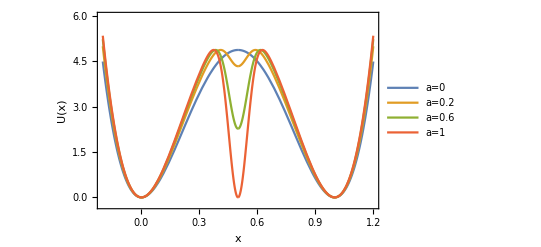

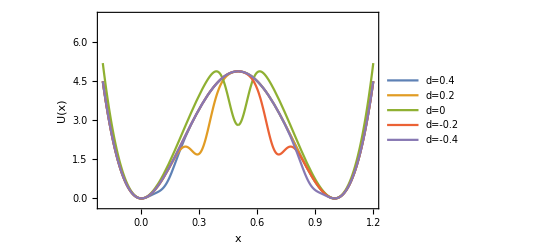

```mathematica
ClearAll[hNorm]

Uper[x_,d_,a_,h_]:=h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

Ushift[x_,d_,a_,h_]:=Uper[x-0.5,d,a,h]

b=200;
c=1;

hNorm[x_,d_,a_,h_]:=Module[{argx,hfind,hNorm},
argx=If[a>0 && d==0,0.4,0.5];
hNorm=If[FindMaxValue[Ushift[x,d,a,h],{x,argx}]<h,hfind/.FindRoot[FindMaxValue[Ushift[x,d,a,hfind],{x,argx}]==h,{hfind,5}],h]];

hNorm0a=hNorm[x,0,0,4.88];hNorm02a=hNorm[x,0,0.2,4.88];hNorm06a=hNorm[x,0,0.6,4.88];hNorm1a=hNorm[x,0,1,4.88];

hNorm04d=hNorm[x,0.4,0.5,4.88];
hNorm02d=hNorm[x,0.2,0.5,4.88];
hNorm0d=hNorm[x,0,0.5,4.88];
hNormMin02d=hNorm[x,-0.2,0.5,4.88];
hNormMin04d=hNorm[x,-0.4,0.5,4.88];

Plot[{Ushift[x,0,0,hNorm0a],Ushift[x,0,0.2,hNorm02a],Ushift[x,0,0.6,hNorm06a],Ushift[x,0,1,hNorm1a]},{x,-0.2,1.2},Frame->True, FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium,PlotRange->{-0.25,6},PlotLegends->Placed[LineLegend[{"a=0","a=0.2","a=0.6","a=1"},LegendLayout->{"Row",1}],{Left,Top}]]

Plot[{Ushift[x,0.4,0.5,hNorm04d],Ushift[x,0.2,0.5,hNorm02d],Ushift[x,0,0.5,hNorm0d],Ushift[x,-0.2,0.5,hNormMin02d],Ushift[x,-0.4,0.5,hNormMin04d]},{x,-0.2,1.2},Frame->True, FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium,PlotRange->{-0.25,7},PlotLegends->Placed[LineLegend[{"d=0.4","d=0.2","d=0","d=-0.2","d=-0.4"},LegendLayout->{"Row",2}],{Left,Top}]]
```

### MFPT: changing a and d with narrower intermediate well (height normalized)

```mathematica
(* b=2500 *)

Uper[x_,d_,a_,h_]:=h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

a=0.2;
b=2500;
c=1;
h=4.88;

aStepsize=-0.1;
dStepsize=-0.1;

Ushift[x_,d_,a_,h_]:=Uper[x-0.5,d,a,h]

τ[x_,d_,a_,h_]:=Module[{argx,hNorm,sol,τ,hfind},
argx=If[a>0 && d==0,0.4,0.5];
hNorm=If[FindMaxValue[Ushift[x,d,a,h],{x,argx}]<h,hfind/.FindRoot[FindMaxValue[Ushift[x,d,a,hfind],{x,argx}]==h,{hfind,5}],h];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,d,a,hNorm]] NIntegrate[Exp[Ushift[y,d,a,hNorm]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ/.sol]

yticks=MapIndexed[{#2[[1]],#}&,Range[1,0,aStepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[0.4,-0.4,dStepsize]];

data=Table[τ[x,d,a,h],{a,1,0,aStepsize},{d,0.4,-0.4,dStepsize}]
dataRounded=SetPrecision[Round[data,0.01],3];
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"d",None},{"a",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]}]
```

FindMaxValue::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindMaxValue::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaxValue::fmgz will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaxValue::nrnum: The function value -1. hfind$156130 is not a real number at {x} = {0.5}.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

FindMaxValue::nrnum: The function value -0.9216 hfind$216652 is not a real number at {x} = {0.4}.

FindMaxValue::nrnum: The function value -1. hfind$288261 is not a real number at {x} = {0.5}.

General::stop: Further output of FindMaxValue::nrnum will be suppressed during this calculation.

{{5.34498,5.59722,5.31003,4.69254,4.49435,4.27252,4.59761,4.73446,4.76128},{5.27361,5.43955,5.12262,4.54197,4.41083,4.25764,4.59737,4.7351,4.76155},{5.20565,5.30615,4.9865,4.4503,4.37012,4.25714,4.6004,4.73622,4.76185},{5.14093,5.19319,4.88865,4.39981,4.3595,4.26828,4.60644,4.73782,4.76218},{5.07928,5.0975,4.81971,4.3795,4.37197,4.28995,4.6155,4.7399,4.76254},{5.02053,5.01642,4.77307,4.38305,4.40465,4.3224,4.6278,4.7425,4.76293},{4.96453,4.94776,4.74419,4.40766,4.45781,4.36721,4.64382,4.74566,4.76334},{4.91115,4.88969,4.73009,4.45349,4.53447,4.42747,4.66428,4.74944,4.76379},{4.86023,4.84071,4.72911,4.52352,4.63985,4.50819,4.69026,4.75391,4.76427},{4.81167,4.79959,4.74069,4.62401,4.77722,4.617,4.72325,4.75917,4.76478},{4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533}}

-Graphics-

```mathematica
(* b=2000 *)

Uper[x_,d_,a_,h_]:=h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

a=0.2;
b=2000;
c=1;
h=4.88;

aStepsize=-0.1;
dStepsize=-0.1;

Ushift[x_,d_,a_,h_]:=Uper[x-0.5,d,a,h]

τ[x_,d_,a_,h_]:=Module[{argx,hNorm,sol,τ,hfind},
argx=If[a>0 && d==0,0.4,0.5];
hNorm=If[FindMaxValue[Ushift[x,d,a,h],{x,argx}]<h,hfind/.FindRoot[FindMaxValue[Ushift[x,d,a,hfind],{x,argx}]==h,{hfind,5}],h];sol=FindRoot[τ==NIntegrate[Exp[-Ushift[x,d,a,hNorm]] NIntegrate[Exp[Ushift[y,d,a,hNorm]],{y,x,1}],{x,0,1}] ,{τ,1}];
τ/.sol]

yticks=MapIndexed[{#2[[1]],#}&,Range[1,0,aStepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[0.4,-0.4,dStepsize]];

data=Table[τ[x,d,a,h],{a,1,0,aStepsize},{d,0.4,-0.4,dStepsize}]
dataRounded=SetPrecision[Round[data,0.01],3];
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"d",None},{"a",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]}]
```

{{5.41084,5.69355,5.36989,4.677,4.48261,4.21033,4.57506,4.73004,4.7607},{5.33125,5.51758,5.16142,4.51123,4.38983,4.19519,4.57526,4.73086,4.76102},{5.25549,5.36871,5.01001,4.4104,4.34474,4.1956,4.57901,4.73219,4.76137},{5.18336,5.24267,4.90119,4.35503,4.33308,4.20869,4.58607,4.73405,4.76174},{5.11468,5.13589,4.82456,4.33301,4.3471,4.23332,4.59645,4.73645,4.76215},{5.04925,5.04543,4.77278,4.33742,4.38357,4.26985,4.61044,4.73943,4.76259},{4.98691,4.96882,4.74077,4.3652,4.44278,4.32011,4.62856,4.74304,4.76307},{4.9275,4.90404,4.72526,4.41659,4.52806,4.38757,4.65164,4.74734,4.76358},{4.87086,4.84941,4.72439,4.49497,4.6449,4.47785,4.6809,4.75241,4.76412},{4.81685,4.80354,4.73755,4.60734,4.79557,4.59951,4.71803,4.75836,4.7647},{4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533,4.76533}}

-Graphics-

#### MFPT: asymmetric well, changing k

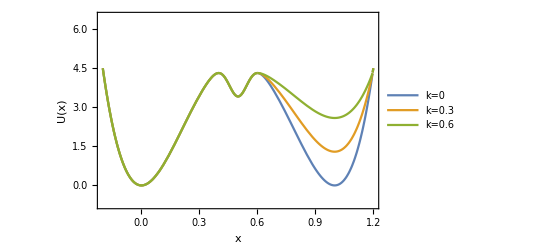

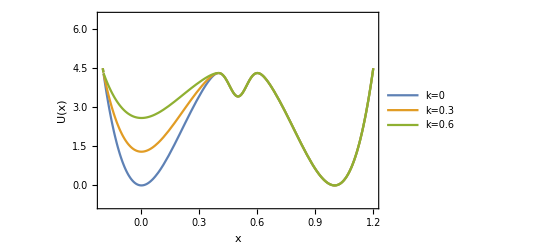

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{3.15499,3.16209,3.16931,3.17667,3.18415,3.19178,3.19955,3.20746,3.21551,3.22372,3.23209,3.24061,3.24931,3.25817,3.2672,3.27642,3.28582,3.2954,3.30518,3.31516,3.32535,3.33575,3.34636,3.35719,3.36826,3.37956,3.3911,3.40289,3.41494,3.42726,3.43984,3.45271,3.46586,3.47931,3.49306,3.50713,3.52153,3.53626,3.55133,3.56675,3.58254,3.59871,3.61527,3.63222,3.64959,3.66738,3.68561,3.70429,3.72343,3.74306,3.76318,3.78382,3.80498,3.82669,3.84895,3.8718,3.89525,3.91931,3.94402,3.96938,3.99542,4.02216,4.04963,4.07785,4.10684,4.13664,4.16726,4.19873,4.23108,4.26435,4.29856,4.33375,4.36994,4.40717,4.44548,4.4849,4.52548,4.56725,4.61024,4.65452,4.70011}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindArgMin::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.15499,3.04898,2.94686,2.84849,2.75374,2.66246,2.57453,2.48982,2.40819,2.32955,2.25377,2.18075,2.11038,2.04257,1.97722,1.91424,1.85353,1.79501,1.73861,1.68423,1.63181,1.58127,1.53255,1.48557,1.44026,1.39658,1.35445,1.31381,1.27463,1.23683,1.20037,1.16519,1.13126,1.09853,1.06694,1.03646,1.00706,0.978675,0.951285,0.924849,0.899333,0.874702,0.850925,0.827969,0.805806,0.784405,0.763741,0.743784,0.724511,0.705896,0.687915,0.670545,0.653765,0.637553,0.621888,0.606751,0.592122,0.577984,0.56432,0.551111,0.538341,0.525996,0.51406,0.502518,0.491356,0.480561,0.47012,0.46002,0.450249,0.440796,0.43165,0.422798,0.414233,0.405942,0.397917,0.390148,0.382627,0.375344,0.368292,0.361463,0.354848}

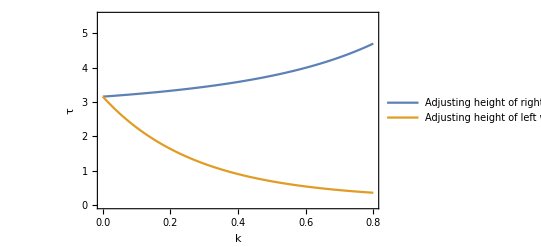

```mathematica
U[x_]:=h(1-(2 x/s[x])^2)^2;
Uas[x_,k_]:=h(1-(2 x/s[x])^2)^2 + 10 k x^3 HeavisideTheta[x];
UPerAsR[x_,k_]:=If[x<0.100365||x>0.696475,h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]),h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2])+(k(4.31483-h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2])))]; 
UPerAsL[x_,k_]:=If[x>-0.100365||x<-0.696475,h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]),h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2])+(k(4.31483-h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2])))]; 
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];

c=1;
h=4.88;
a=0.3;
b=200;
d=0;

kMin=0;
kMax=0.8;
kStepsize=0.01;

Plot[{UPerAsR[x-0.5,0],UPerAsR[x-0.5,0.3],UPerAsR[x-0.5,0.6]},{x,-0.2,1.2},Axes->False,PlotRange->{-0.75,6.5},LabelStyle->Medium,Frame->True,FrameLabel->{"x","U(x)"},PlotLegends->Placed[LineLegend[{"k=0","k=0.3","k=0.6"},LegendLayout->"Row"],{0.5,0.9}]]
Plot[{UPerAsL[x-0.5,0],UPerAsL[x-0.5,0.3],UPerAsL[x-0.5,0.6]},{x,-0.2,1.2},Axes->False,PlotRange->{-0.75,6.5},LabelStyle->Medium,Frame->True,FrameLabel->{"x","U(x)"},PlotLegends->Placed[LineLegend[{"k=0","k=0.3","k=0.6"},LegendLayout->"Row"],{0.5,0.9}]]

(* varying k: adjusting right well *)
τkPerR={};
Do[Ushift[x_,k_]:=UPerAsR[x-0.5,k];
sol=FindRoot[τ==NIntegrate[Exp[Ushift[x,k]] NIntegrate[Exp[-Ushift[y,k]],{y,0,x}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τkPerR,τ],{k,kMin,kMax,kStepsize}]
Print[τkPerR]

(* varying k: adjusting left well *)
τkPerL={};
Do[min=First[FindArgMin[UPerAsL[x,k],{x,-0.4}]];
Ushift[x_,k_]:=UPerAsL[x+min,k];
sol=FindRoot[τ==NIntegrate[Exp[Ushift[x,k]] NIntegrate[Exp[-Ushift[y,k]],{y,0,x}],{x,0,1}] ,{τ,1}];
τ=τ/.sol;AppendTo[τkPerL,τ],{k,kMin,kMax,kStepsize}]
Print[τkPerL]

ListLinePlot[{Transpose@{Range[kMin,kMax,kStepsize],τkPerR},Transpose@{Range[kMin,kMax,kStepsize],τkPerL}},PlotRange->{0,5.5},Frame->True,FrameLabel->{"k","τ"},LabelStyle->Medium,PlotLegends->Placed[{"Adjusting height of right well","Adjusting height of left well"},{Left,Top}]]
```